### PARAMETRES

```mathematica
ClearAll
listH ={100,10,10} (*мощности слоев*)
slope = 10 Degree (*наклон слоев*)
len = 1000(*длина профиля*)
dx = 10(*шаг по профилю*)
hDispersion = 100(*степень складчатости нижнего слоя в метрах*)
hTapering =2  (*степень влияния нижнего горизонта на верхние*)
listV = {2700,2500,3000, 3500} (*набор скоростей*)
wellCount= 10 (*кол скважин*)
wellType = "regular" (*расположение скважин "max","min","regular","random"*)
type = 1 (*выполаживание. 1 - кверху, -1 - книзу*)
velocityTrend = 1(*1 or 0*)
velocityAnomaly =1 (*1 or 0*)
```

ClearAll

{100,10,10}

10 °

1000

10

100

2

{2700,2500,3000,3500}

10

regular

1

1

1

### DEPTH

```mathematica
horizons = BuildDepthSection[listH,slope,len,dx,hDispersion,hTapering, type][["horizons"]]
```

{{{0,-134},{10,-134},{20,-133},{30,-133},{40,-131},{50,-128},{60,-129},{70,-128},{80,-131},{90,-132},{100,-136},{110,-143},{120,-153},{130,-162},{140,-173},{150,-183},{160,-192},{170,-197},{180,-200},{190,-200},{200,-201},{210,-197},{220,-196},{230,-192},{240,-193},{250,-195},{260,-195},{270,-193},{280,-194},{290,-190},{300,-186},{310,-177},{320,-169},{330,-160},{340,-152},{350,-144},{360,-138},{370,-129},{380,-126},{390,-123},{400,-119},{410,-115},{420,-110},{430,-100},{440,-93},{450,-83},{460,-74},{470,-68},{480,-64},{490,-59},{500,-56},{510,-62},{520,-72},{530,-75},{540,-80},{550,-84},{560,-92},{570,-92},{580,-93},{590,-88},{600,-85},{610,-83},{620,-78},{630,-72},{640,-68},{650,-64},{660,-52},{670,-46},{680,-37},{690,-27},{700,-21},{710,-16},{720,-15},{730,-16},{740,-17},{750,-21},{760,-23},{770,-24},{780,-24},{790,-22},{800,-18},{810,-12},{820,-9},{830,-12},{840,-15},{850,-19},{860,-29},{870,-41},{880,-48},{890,-55},{900,-58},{910,-55},{920,-46},{930,-32},{940,-15},{950,3},{960,18},{970,37},{980,50},{990,60},{1000,66}},{{0,-235},{10,-234},{20,-234},{30,-233},{40,-232},{50,-230},{60,-231},{70,-229},{80,-232},{90,-232},{100,-236},{110,-243},{120,-253},{130,-263},{140,-274},{150,-285},{160,-294},{170,-299},{180,-301},{190,-302},{200,-302},{210,-298},{220,-297},{230,-293},{240,-293},{250,-295},{260,-296},{270,-295},{280,-295},{290,-292},{300,-288},{310,-279},{320,-270},{330,-261},{340,-253},{350,-245},{360,-239},{370,-230},{380,-227},{390,-224},{400,-221},{410,-217},{420,-211},{430,-202},{440,-194},{450,-184},{460,-176},{470,-169},{480,-164},{490,-159},{500,-157},{510,-162},{520,-173},{530,-176},{540,-182},{550,-186},{560,-194},{570,-193},{580,-194},{590,-190},{600,-186},{610,-184},{620,-179},{630,-174},{640,-170},{650,-165},{660,-154},{670,-147},{680,-138},{690,-128},{700,-121},{710,-116},{720,-115},{730,-116},{740,-118},{750,-122},{760,-125},{770,-126},{780,-126},{790,-123},{800,-119},{810,-112},{820,-109},{830,-112},{840,-115},{850,-120},{860,-129},{870,-142},{880,-150},{890,-157},{900,-160},{910,-157},{920,-148},{930,-134},{940,-116},{950,-98},{960,-82},{970,-63},{980,-50},{990,-41},{1000,-35}},{{0,-246},{10,-245},{20,-244},{30,-244},{40,-243},{50,-241},{60,-242},{70,-241},{80,-243},{90,-243},{100,-246},{110,-253},{120,-263},{130,-274},{140,-286},{150,-297},{160,-306},{170,-311},{180,-313},{190,-313},{200,-313},{210,-309},{220,-308},{230,-304},{240,-304},{250,-306},{260,-307},{270,-306},{280,-307},{290,-303},{300,-299},{310,-290},{320,-281},{330,-272},{340,-263},{350,-255},{360,-249},{370,-241},{380,-238},{390,-235},{400,-232},{410,-228},{420,-222},{430,-213},{440,-205},{450,-195},{460,-187},{470,-180},{480,-174},{490,-169},{500,-167},{510,-173},{520,-183},{530,-188},{540,-194},{550,-198},{560,-205},{570,-205},{580,-205},{590,-201},{600,-196},{610,-195},{620,-190},{630,-185},{640,-181},{650,-176},{660,-166},{670,-158},{680,-149},{690,-139},{700,-132},{710,-126},{720,-125},{730,-126},{740,-129},{750,-134},{760,-137},{770,-138},{780,-138},{790,-135},{800,-130},{810,-123},{820,-120},{830,-122},{840,-125},{850,-130},{860,-140},{870,-153},{880,-161},{890,-169},{900,-172},{910,-170},{920,-161},{930,-146},{940,-128},{950,-109},{960,-92},{970,-74},{980,-61},{990,-51},{1000,-45}},{{0,-274},{10,-270},{20,-267},{30,-267},{40,-270},{50,-274},{60,-276},{70,-273},{80,-270},{90,-263},{100,-260},{110,-263},{120,-278},{130,-300},{140,-323},{150,-338},{160,-346},{170,-349},{180,-349},{190,-343},{200,-341},{210,-334},{220,-334},{230,-330},{240,-327},{250,-326},{260,-332},{270,-340},{280,-343},{290,-342},{300,-337},{310,-326},{320,-314},{330,-297},{340,-282},{350,-272},{360,-268},{370,-268},{380,-266},{390,-265},{400,-266},{410,-261},{420,-255},{430,-241},{440,-233},{450,-226},{460,-219},{470,-207},{480,-191},{490,-180},{500,-182},{510,-187},{520,-200},{530,-218},{540,-236},{550,-243},{560,-244},{570,-238},{580,-234},{590,-227},{600,-222},{610,-218},{620,-218},{630,-218},{640,-212},{650,-206},{660,-201},{670,-193},{680,-180},{690,-167},{700,-152},{710,-138},{720,-135},{730,-140},{740,-148},{750,-167},{760,-179},{770,-186},{780,-183},{790,-169},{800,-151},{810,-141},{820,-136},{830,-133},{840,-141},{850,-153},{860,-163},{870,-178},{880,-194},{890,-211},{900,-222},{910,-221},{920,-210},{930,-188},{940,-160},{950,-128},{960,-105},{970,-88},{980,-77},{990,-69},{1000,-66}}}

```mathematica
PlotDepthSection[horizons, Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]]
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
PlotVelocity[velModel, horizons, {PlotStyle -> {Directive[Thickness[0.005], Black]},
							PlotLabel->"Velocity Distribution",
							PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
							ImageSize -> 500, 
ColorFunction -> ColorData[{"RedBlueTones", "Reverse"}],
						PlotLegends -> BarLegend[Automatic, LegendLabel -> "Vel, m/s"],
						PlotLabel -> "Velocity Distribution",
						Contours -> {Automatic, 20},
GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None}}]
```

-Graphics-

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]]
```

{{{0,0},{10,0},{20,0},{30,0},{40,0},{50,0},{60,0},{70,0},{80,0},{90,0},{100,0},{110,0},{120,0},{130,0},{140,0},{150,0},{160,0},{170,0},{180,0},{190,0},{200,0},{210,0},{220,0},{230,0},{240,0},{250,0},{260,0},{270,0},{280,0},{290,0},{300,0},{310,0},{320,0},{330,0},{340,0},{350,0},{360,0},{370,0},{380,0},{390,0},{400,0},{410,0},{420,0},{430,0},{440,0},{450,0},{460,0},{470,0},{480,0},{490,0},{500,0},{510,0},{520,0},{530,0},{540,0},{550,0},{560,0},{570,0},{580,0},{590,0},{600,0},{610,0},{620,0},{630,0},{640,0},{650,0},{660,0},{670,0},{680,0},{690,0},{700,0},{710,0},{720,0},{730,0},{740,0},{750,0},{760,0},{770,0},{780,0},{790,0},{800,0},{810,0},{820,0},{830,0},{840,0},{850,0},{860,0},{870,0},{880,0},{890,0},{900,0},{910,0},{920,0},{930,0},{940,0},{950,0},{960,0},{970,0},{980,0},{990,0},{1000,0}},{{0,0.252314},{10,0.252444},{20,0.252077},{30,0.25094},{40,0.24852},{50,0.245456},{60,0.246619},{70,0.243726},{80,0.248452},{90,0.249232},{100,0.25517},{110,0.26424},{120,0.27793},{130,0.289372},{140,0.303797},{150,0.317589},{160,0.330081},{170,0.335921},{180,0.339439},{190,0.341246},{200,0.342084},{210,0.336561},{220,0.334776},{230,0.330261},{240,0.330263},{250,0.333284},{260,0.333475},{270,0.332317},{280,0.331597},{290,0.327842},{300,0.322359},{310,0.310461},{320,0.299234},{330,0.287831},{340,0.277871},{350,0.266593},{360,0.258959},{370,0.246135},{380,0.242153},{390,0.238217},{400,0.233542},{410,0.227945},{420,0.220437},{430,0.208308},{440,0.198549},{450,0.184681},{460,0.173523},{470,0.165017},{480,0.159431},{490,0.152545},{500,0.149376},{510,0.156127},{520,0.170665},{530,0.173727},{540,0.18119},{550,0.186241},{560,0.197689},{570,0.195807},{580,0.198329},{590,0.192234},{600,0.188012},{610,0.185007},{620,0.178328},{630,0.171052},{640,0.165658},{650,0.159174},{660,0.143745},{670,0.135317},{680,0.123404},{690,0.110236},{700,0.10177},{710,0.0954985},{720,0.0938189},{730,0.0953432},{740,0.0970221},{750,0.102104},{760,0.105173},{770,0.106724},{780,0.106705},{790,0.103461},{800,0.0982128},{810,0.0895987},{820,0.0856323},{830,0.0903274},{840,0.0940865},{850,0.100062},{860,0.112141},{870,0.128787},{880,0.13874},{890,0.147982},{900,0.151708},{910,0.147793},{920,0.135551},{930,0.117355},{940,0.0941344},{950,0.0740329},{960,0.0713758},{970,0.0685072},{980,0.0666587},{990,0.065944},{1000,0.0650571}},{{0,0.399204},{10,0.399824},{20,0.399361},{30,0.398326},{40,0.39382},{50,0.388172},{60,0.389709},{70,0.386515},{80,0.393909},{90,0.396955},{100,0.406694},{110,0.422577},{120,0.439593},{130,0.4538},{140,0.471743},{150,0.490786},{160,0.509447},{170,0.518503},{180,0.523795},{190,0.527508},{200,0.528798},{210,0.5222},{220,0.519432},{230,0.512576},{240,0.513665},{250,0.519149},{260,0.517936},{270,0.512912},{280,0.512464},{290,0.505691},{300,0.498019},{310,0.481302},{320,0.465832},{330,0.45087},{340,0.437907},{350,0.422376},{360,0.410668},{370,0.390446},{380,0.384208},{390,0.378201},{400,0.370616},{410,0.362794},{420,0.351528},{430,0.33535},{440,0.32109},{450,0.300361},{460,0.284516},{470,0.272584},{480,0.265924},{490,0.258098},{500,0.251747},{510,0.263043},{520,0.282635},{530,0.285619},{540,0.294348},{550,0.30129},{560,0.317816},{570,0.317035},{580,0.320552},{590,0.31283},{600,0.305625},{610,0.302708},{620,0.291946},{630,0.280599},{640,0.273206},{650,0.263824},{660,0.241671},{670,0.228469},{680,0.21186},{690,0.193272},{700,0.181718},{710,0.173759},{720,0.171875},{730,0.173046},{740,0.175539},{750,0.181327},{760,0.185119},{770,0.186515},{780,0.186783},{790,0.183282},{800,0.176844},{810,0.164772},{820,0.159502},{830,0.166172},{840,0.170669},{850,0.178541},{860,0.196722},{870,0.220763},{880,0.233991},{890,0.246561},{900,0.2508},{910,0.245753},{920,0.228617},{930,0.202683},{940,0.17007},{950,0.140324},{960,0.128315},{970,0.114095},{980,0.104005},{990,0.097068},{1000,0.0923103}},{{0,0.533651},{10,0.531692},{20,0.529416},{30,0.528439},{40,0.525798},{50,0.522479},{60,0.52533},{70,0.520232},{80,0.525774},{90,0.524579},{100,0.532563},{110,0.550329},{120,0.57648},{130,0.60491},{140,0.640001},{150,0.67227},{160,0.700544},{170,0.716152},{180,0.719259},{190,0.714111},{200,0.713252},{210,0.699848},{220,0.696737},{230,0.686417},{240,0.68502},{250,0.689557},{260,0.693801},{270,0.696398},{280,0.699545},{290,0.691707},{300,0.678747},{310,0.651892},{320,0.626977},{330,0.600114},{340,0.577271},{350,0.555474},{360,0.541353},{370,0.521205},{380,0.513606},{390,0.507104},{400,0.500075},{410,0.489299},{420,0.474439},{430,0.450254},{440,0.43157},{450,0.40692},{460,0.387281},{470,0.368975},{480,0.353929},{490,0.340551},{500,0.335135},{510,0.349014},{520,0.375346},{530,0.387851},{540,0.406516},{550,0.417452},{560,0.434449},{570,0.43027},{580,0.431573},{590,0.419955},{600,0.409996},{610,0.404998},{620,0.394165},{630,0.382849},{640,0.37215},{650,0.359706},{660,0.33489},{670,0.31748},{680,0.294252},{690,0.269153},{700,0.250216},{710,0.235503},{720,0.232179},{730,0.235767},{740,0.242109},{750,0.257218},{760,0.266965},{770,0.271999},{780,0.270663},{790,0.260223},{800,0.244881},{810,0.227921},{820,0.220303},{830,0.22553},{840,0.233882},{850,0.247536},{860,0.270683},{870,0.302181},{880,0.323589},{890,0.345034},{900,0.355121},{910,0.349598},{920,0.326559},{930,0.289178},{940,0.242504},{950,0.197335},{960,0.174557},{970,0.152526},{980,0.137483},{990,0.126953},{1000,0.12087}}}

```mathematica
PlotTimeSection[time, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"}]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]]
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]]
```

{50,150,250,350,450,550,650,750,850,950}

```mathematica
PlotDepthSection[horizons, wellDataset,{GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
											Filling -> Bottom, Frame -> True, ImageSize -> 500,
											PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

```mathematica
Clear[t]
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]]
resultHT=HTMethod[wellDataset, time, t][["result"]]
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]]
```

{FittedModel[-45.0665-1503.03 t],FittedModel[-38.6155-1037.75 t],FittedModel[-56.3961-811.619 t]}

{{-45.0665,-1503.03},{-38.6155,-1037.75},{-56.3961,-811.619}}

{{{40,-131.},{140,-173.},{240,-193.},{340,-152.},{440,-93.},{540,-80.},{640,-68.},{740,-17.},{840,-15.},{940,-15.}},{{0,-233.912},{10,-234.296},{20,-234.271},{30,-233.634},{40,-232.},{50,-229.852},{60,-230.852},{70,-228.777},{80,-232.402},{90,-233.039},{100,-237.529},{110,-244.354},{120,-254.631},{130,-263.202},{140,-274.},{150,-284.309},{160,-293.629},{170,-297.939},{180,-300.497},{190,-301.762},{200,-302.293},{210,-298.041},{220,-296.596},{230,-293.1},{240,-293.},{250,-295.172},{260,-295.222},{270,-294.265},{280,-293.643},{290,-290.749},{300,-286.566},{310,-277.572},{320,-269.094},{330,-260.498},{340,-253.},{350,-244.527},{360,-238.807},{370,-229.201},{380,-226.254},{390,-223.353},{400,-219.909},{410,-215.785},{420,-210.234},{430,-201.222},{440,-194.},{450,-183.698},{460,-175.438},{470,-169.174},{480,-165.102},{490,-160.049},{500,-157.782},{510,-162.958},{520,-173.972},{530,-176.343},{540,-182.},{550,-185.821},{560,-194.427},{570,-192.998},{580,-194.864},{590,-190.242},{600,-187.019},{610,-184.706},{620,-179.629},{630,-174.105},{640,-170.},{650,-165.083},{660,-153.449},{670,-147.081},{680,-138.095},{690,-128.166},{700,-121.768},{710,-117.016},{720,-115.709},{730,-116.801},{740,-118.},{750,-121.745},{760,-123.968},{770,-125.044},{780,-124.938},{790,-122.407},{800,-118.373},{810,-111.815},{820,-108.759},{830,-112.224},{840,-115.},{850,-119.459},{860,-128.526},{870,-141.048},{880,-148.567},{890,-155.581},{900,-158.482},{910,-155.676},{920,-146.65},{930,-133.191},{940,-116.},{950,-101.2},{960,-99.5604},{970,-97.8146},{980,-96.8914},{990,-96.8793},{1000,-96.7997}},{{0,-240.833},{10,-242.668},{20,-243.753},{30,-244.361},{40,-243.},{50,-240.886},{60,-242.349},{70,-241.218},{80,-245.45},{90,-247.304},{100,-252.52},{110,-260.821},{120,-269.619},{130,-276.876},{140,-286.},{150,-295.63},{160,-305.009},{170,-309.361},{180,-311.725},{190,-313.245},{200,-313.493},{210,-309.643},{220,-307.785},{230,-303.819},{240,-304.},{250,-306.494},{260,-305.547},{270,-302.661},{280,-302.189},{290,-298.476},{300,-294.339},{310,-285.555},{320,-277.465},{330,-269.689},{340,-263.},{350,-255.031},{360,-249.094},{370,-238.786},{380,-235.774},{390,-232.918},{400,-229.277},{410,-225.541},{420,-220.042},{430,-212.015},{440,-205.},{450,-194.639},{460,-186.815},{470,-181.014},{480,-177.93},{490,-174.215},{500,-171.228},{510,-177.351},{520,-187.722},{530,-189.409},{540,-194.},{550,-197.582},{560,-206.063},{570,-205.502},{580,-207.123},{590,-202.875},{600,-198.872},{610,-197.082},{620,-191.222},{630,-185.073},{640,-181.},{650,-175.93},{660,-164.266},{670,-157.272},{680,-148.529},{690,-138.773},{700,-132.674},{710,-128.441},{720,-127.355},{730,-127.843},{740,-129.},{750,-131.844},{760,-133.637},{770,-134.177},{780,-134.129},{790,-132.131},{800,-128.62},{810,-122.206},{820,-119.347},{830,-122.717},{840,-125.},{850,-129.082},{860,-138.569},{870,-151.158},{880,-158.206},{890,-164.989},{900,-167.532},{910,-165.349},{920,-156.99},{930,-144.172},{940,-128.},{950,-113.435},{960,-108.2},{970,-101.952},{980,-97.9869},{990,-95.8061},{1000,-94.9113}},{{0,-254.908},{10,-259.803},{20,-263.793},{30,-267.578},{40,-270.},{50,-271.502},{60,-274.906},{70,-274.527},{80,-277.951},{90,-278.171},{100,-281.689},{110,-288.793},{120,-298.96},{130,-309.755},{140,-323.},{150,-334.891},{160,-344.995},{170,-349.837},{180,-349.527},{190,-345.833},{200,-343.888},{210,-336.903},{220,-334.192},{230,-328.694},{240,-327.},{250,-327.931},{260,-328.955},{270,-329.508},{280,-330.468},{290,-327.14},{300,-321.888},{310,-311.137},{320,-301.301},{330,-290.786},{340,-282.},{350,-273.725},{360,-268.652},{370,-261.225},{380,-258.987},{390,-257.293},{400,-255.489},{410,-252.272},{420,-247.509},{430,-239.078},{440,-233.},{450,-224.615},{460,-218.335},{470,-212.616},{480,-208.188},{490,-204.352},{500,-203.611},{510,-210.511},{520,-222.225},{530,-228.035},{540,-236.},{550,-240.448},{560,-247.006},{570,-244.667},{580,-244.296},{590,-238.471},{600,-233.156},{610,-229.738},{620,-223.88},{630,-217.804},{640,-212.},{650,-205.55},{660,-194.146},{670,-185.813},{680,-175.182},{690,-163.853},{700,-155.083},{710,-148.084},{720,-145.762},{730,-146.297},{740,-148.},{750,-153.312},{760,-156.51},{770,-157.872},{780,-156.741},{790,-152.021},{800,-145.431},{810,-138.32},{820,-135.148},{830,-137.351},{840,-141.},{850,-146.992},{860,-157.042},{870,-170.702},{880,-180.502},{890,-190.565},{900,-196.283},{910,-195.944},{920,-188.789},{930,-176.12},{940,-160.},{950,-144.826},{960,-139.088},{970,-134.017},{980,-132.159},{990,-132.526},{1000,-135.103}}}

{{{0.12426,-232.},{0.151898,-274.},{0.165131,-293.},{0.138935,-253.},{0.0992746,-194.},{0.090595,-182.},{0.0828291,-170.},{0.048511,-118.},{0.0470433,-115.},{0.0470672,-116.}},{{0.19691,-243.},{0.235872,-286.},{0.256832,-304.},{0.218954,-263.},{0.160545,-205.},{0.147174,-194.},{0.136603,-181.},{0.0877697,-129.},{0.0853343,-125.},{0.0850351,-128.}},{{0.262899,-270.},{0.32,-323.},{0.34251,-327.},{0.288636,-282.},{0.215785,-233.},{0.203258,-236.},{0.186075,-212.},{0.121055,-148.},{0.116941,-141.},{0.121252,-160.}}}

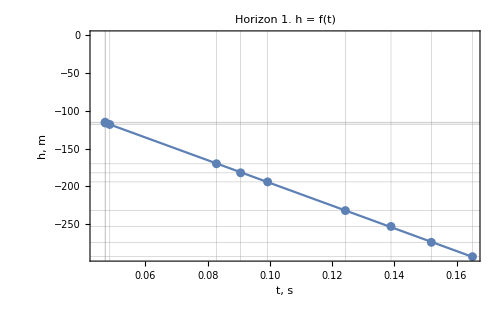
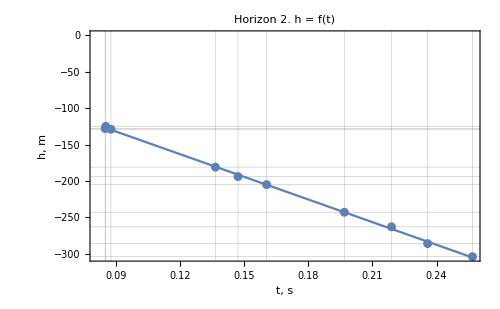
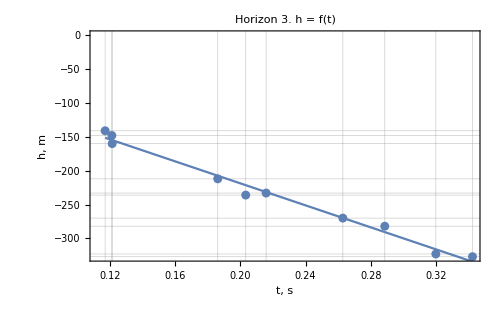

```mathematica
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

```mathematica
lmSetVT=VTMethod[wellDataset,datasetVelModel,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,datasetVelModel,time, t][["lmParametres"]]
wellValuesVT=VTMethod[wellDataset,datasetVelModel,time, t][["wellValues"]]
resultVT = VTMethod[wellDataset,datasetVelModel,time, t][["result"]]
fitsVT = VTMethod[wellDataset,datasetVelModel,time, t][["fits"]]
```

{FittedModel[2492.14+9.6744 t],FittedModel[3004.12-23.7268 t],FittedModel[3480.12+59.1111 t]}

{{2492.14,9.6744},{3004.12,-23.7268},{3480.12,59.1111}}

{{{1,0.12426,2481},{1,0.151898,2490},{1,0.165131,2492},{1,0.138935,2498},{1,0.0992746,2511},{1,0.090595,2505},{1,0.0828291,2484},{1,0.048511,2481},{1,0.0470433,2486},{1,0.0470672,2503}},{{2,0.19691,3015},{2,0.235872,2999},{2,0.256832,2982},{2,0.218954,2994},{2,0.160545,3011},{2,0.147174,3000},{2,0.136603,3018},{2,0.0877697,2985},{2,0.0853343,2997},{2,0.0850351,3002}},{{3,0.262899,3485},{3,0.32,3511},{3,0.34251,3479},{3,0.288636,3519},{3,0.215785,3494},{3,0.203258,3465},{3,0.186075,3526},{3,0.121055,3513},{3,0.116941,3470},{3,0.121252,3468}}}

{{{40,-131.},{140,-173.},{240,-193.},{340,-152.},{440,-93.},{540,-80.},{640,-68.},{740,-17.},{840,-15.},{940,-15.}},{{0,-242.751},{10,-241.911},{20,-240.092},{30,-236.989},{40,-232.},{50,-225.961},{60,-224.99},{70,-218.784},{80,-221.956},{90,-220.107},{100,-224.638},{110,-233.06},{120,-247.268},{130,-258.725},{140,-274.},{150,-288.617},{160,-301.78},{170,-306.837},{180,-309.236},{190,-309.779},{200,-309.429},{210,-301.485},{220,-298.607},{230,-292.747},{240,-293.},{250,-297.519},{260,-298.979},{270,-299.203},{280,-300.392},{290,-298.179},{300,-294.171},{310,-282.481},{320,-271.933},{330,-261.443},{340,-253.},{350,-243.122},{360,-237.94},{370,-226.353},{380,-225.809},{390,-225.252},{400,-223.633},{410,-220.653},{420,-215.004},{430,-203.235},{440,-194.},{450,-179.16},{460,-167.252},{470,-158.245},{480,-152.52},{490,-144.854},{500,-141.552},{510,-150.396},{520,-168.771},{530,-172.687},{540,-182.},{550,-188.255},{560,-202.502},{570,-200.188},{580,-203.502},{590,-196.259},{600,-191.609},{610,-188.799},{620,-181.783},{630,-174.465},{640,-170.},{650,-164.71},{660,-148.707},{670,-141.764},{680,-130.679},{690,-118.115},{700,-111.381},{710,-107.23},{720,-108.528},{730,-113.426},{740,-118.},{750,-126.213},{760,-131.342},{770,-134.071},{780,-134.397},{790,-130.32},{800,-123.427},{810,-112.084},{820,-106.349},{830,-111.288},{840,-115.},{850,-121.478},{860,-135.636},{870,-155.622},{880,-167.455},{890,-178.661},{900,-183.309},{910,-178.811},{920,-164.375},{930,-143.03},{940,-116.},{950,-93.5059},{960,-93.469},{970,-93.9383},{980,-96.5132},{990,-101.399},{1000,-107.032}},{{0,-260.935},{10,-261.222},{20,-258.585},{30,-253.913},{40,-243.},{50,-229.443},{60,-225.795},{70,-214.393},{80,-218.227},{90,-215.121},{100,-221.679},{110,-237.2},{120,-254.325},{130,-267.297},{140,-286.},{150,-306.621},{160,-327.075},{170,-333.745},{180,-335.463},{190,-335.605},{200,-333.04},{210,-319.746},{220,-313.304},{230,-302.038},{240,-304.},{250,-313.989},{260,-315.426},{270,-312.525},{280,-317.695},{290,-314.604},{300,-311.252},{310,-295.41},{320,-282.324},{330,-270.808},{340,-263.},{350,-251.98},{360,-247.096},{370,-229.734},{380,-233.264},{390,-236.958},{400,-237.905},{410,-237.903},{420,-231.953},{430,-217.654},{440,-205.},{450,-181.305},{460,-163.605},{470,-150.571},{480,-144.364},{490,-135.477},{500,-127.981},{510,-146.191},{520,-176.234},{530,-180.987},{540,-194.},{550,-204.143},{560,-228.587},{570,-227.321},{580,-232.823},{590,-222.053},{600,-212.766},{610,-210.782},{620,-198.147},{630,-185.896},{640,-181.},{650,-174.667},{660,-150.516},{670,-140.697},{680,-126.382},{690,-109.365},{700,-102.803},{710,-101.213},{720,-107.969},{730,-118.21},{740,-129.},{750,-143.038},{760,-152.492},{770,-156.943},{780,-158.465},{790,-153.282},{800,-142.815},{810,-123.204},{820,-113.253},{830,-120.841},{840,-125.},{850,-134.221},{860,-159.062},{870,-193.029},{880,-211.34},{890,-229.38},{900,-235.848},{910,-229.496},{920,-206.303},{930,-171.359},{940,-128.},{950,-90.6958},{960,-81.9261},{970,-71.9761},{980,-70.5322},{990,-76.3096},{1000,-88.0275}},{{0,-314.906},{10,-306.67},{20,-295.736},{30,-285.188},{40,-270.},{50,-252.14},{60,-243.955},{70,-220.66},{80,-215.4},{90,-197.62},{100,-195.729},{110,-211.03},{120,-241.299},{130,-275.947},{140,-323.},{150,-365.839},{160,-402.577},{170,-417.961},{180,-412.466},{190,-393.877},{200,-384.774},{210,-355.377},{220,-346.603},{230,-327.493},{240,-327.},{250,-339.943},{260,-355.1},{270,-369.85},{280,-387.892},{290,-388.473},{300,-381.835},{310,-352.171},{320,-327.475},{330,-300.622},{340,-282.},{350,-266.087},{360,-264.305},{370,-252.021},{380,-261.789},{390,-272.975},{400,-282.361},{410,-283.907},{420,-276.68},{430,-251.089},{440,-233.},{450,-201.913},{460,-177.349},{470,-153.046},{480,-132.633},{490,-113.539},{500,-107.076},{510,-133.424},{520,-180.812},{530,-203.185},{540,-236.},{550,-255.008},{560,-284.823},{570,-277.646},{580,-280.828},{590,-262.177},{600,-247.728},{610,-243.593},{620,-231.019},{630,-219.746},{640,-212.},{650,-203.77},{660,-175.925},{670,-162.713},{680,-140.294},{690,-115.046},{700,-100.496},{710,-92.646},{720,-103.476},{730,-124.549},{740,-148.},{750,-183.953},{760,-207.774},{770,-220.891},{780,-220.688},{790,-202.671},{800,-174.523},{810,-142.32},{820,-125.574},{830,-130.714},{840,-141.},{850,-160.559},{860,-197.059},{870,-248.834},{880,-283.777},{890,-319.974},{900,-337.655},{910,-329.612},{920,-292.805},{930,-233.185},{940,-160.},{950,-92.5405},{960,-67.6368},{970,-47.6326},{980,-43.7279},{990,-51.8826},{1000,-72.2691}}}

{{{0,-314.709},{10,-314.871},{20,-314.413},{30,-312.993},{40,-309.971},{50,-306.146},{60,-307.598},{70,-303.986},{80,-309.886},{90,-310.861},{100,-318.274},{110,-329.599},{120,-346.694},{130,-360.982},{140,-378.998},{150,-396.225},{160,-411.831},{170,-419.126},{180,-423.521},{190,-425.78},{200,-426.827},{210,-419.926},{220,-417.696},{230,-412.055},{240,-412.058},{250,-415.832},{260,-416.07},{270,-414.624},{280,-413.725},{290,-409.033},{300,-402.184},{310,-387.322},{320,-373.299},{330,-359.058},{340,-346.62},{350,-332.537},{360,-323.005},{370,-306.994},{380,-302.023},{390,-297.109},{400,-291.273},{410,-284.287},{420,-274.914},{430,-259.776},{440,-247.597},{450,-230.291},{460,-216.367},{470,-205.754},{480,-198.785},{490,-190.194},{500,-186.24},{510,-194.663},{520,-212.801},{530,-216.621},{540,-225.934},{550,-232.237},{560,-246.523},{570,-244.174},{580,-247.321},{590,-239.715},{600,-234.446},{610,-230.697},{620,-222.363},{630,-213.284},{640,-206.554},{650,-198.465},{660,-179.216},{670,-168.703},{680,-153.844},{690,-137.42},{700,-126.862},{710,-119.042},{720,-116.947},{730,-118.848},{740,-120.942},{750,-127.279},{760,-131.106},{770,-133.041},{780,-133.017},{790,-128.972},{800,-122.427},{810,-111.685},{820,-106.739},{830,-112.594},{840,-117.281},{850,-124.732},{860,-139.797},{870,-160.558},{880,-172.973},{890,-184.501},{900,-189.15},{910,-184.266},{920,-168.994},{930,-146.299},{940,-117.341},{950,-92.2766},{960,-88.9638},{970,-85.3873},{980,-83.0828},{990,-82.1918},{1000,-81.0861}},{{0,-597.739},{10,-598.664},{20,-597.972},{30,-596.427},{40,-589.702},{50,-581.271},{60,-583.565},{70,-578.797},{80,-589.835},{90,-594.381},{100,-608.917},{110,-632.617},{120,-658.003},{130,-679.192},{140,-705.947},{150,-734.333},{160,-762.141},{170,-775.633},{180,-783.518},{190,-789.047},{200,-790.97},{210,-781.141},{220,-777.018},{230,-766.803},{240,-768.426},{250,-776.596},{260,-774.789},{270,-767.305},{280,-766.637},{290,-756.545},{300,-745.112},{310,-720.197},{320,-697.134},{330,-674.823},{340,-655.489},{350,-632.319},{360,-614.847},{370,-584.666},{380,-575.352},{390,-566.385},{400,-555.058},{410,-543.378},{420,-526.551},{430,-502.382},{440,-481.074},{450,-450.091},{460,-426.401},{470,-408.556},{480,-398.595},{490,-386.889},{500,-377.388},{510,-394.285},{520,-423.588},{530,-428.05},{540,-441.101},{550,-451.479},{560,-476.181},{570,-475.014},{580,-480.27},{590,-468.728},{600,-457.959},{610,-453.598},{620,-437.509},{630,-420.543},{640,-409.487},{650,-395.453},{660,-362.312},{670,-342.556},{680,-317.695},{690,-289.864},{700,-272.559},{710,-260.639},{720,-257.816},{730,-259.57},{740,-263.305},{750,-271.974},{760,-277.653},{770,-279.744},{780,-280.146},{790,-274.903},{800,-265.259},{810,-247.176},{820,-239.281},{830,-249.274},{840,-256.009},{850,-267.801},{860,-295.029},{870,-331.022},{880,-350.819},{890,-369.628},{900,-375.97},{910,-368.419},{920,-342.777},{930,-303.955},{940,-255.113},{950,-210.541},{960,-192.542},{970,-171.224},{980,-156.094},{990,-145.69},{1000,-138.555}},{{0,-937.002},{10,-933.533},{20,-929.501},{30,-927.77},{40,-923.092},{50,-917.214},{60,-922.264},{70,-913.234},{80,-923.049},{90,-920.933},{100,-935.075},{110,-966.557},{120,-1012.93},{130,-1063.4},{140,-1125.75},{150,-1183.15},{160,-1233.49},{170,-1261.31},{180,-1266.84},{190,-1257.67},{200,-1256.14},{210,-1232.26},{220,-1226.71},{230,-1208.33},{240,-1205.85},{250,-1213.92},{260,-1221.48},{270,-1226.11},{280,-1231.71},{290,-1217.75},{300,-1194.68},{310,-1146.89},{320,-1102.6},{330,-1054.88},{340,-1014.34},{350,-975.679},{360,-950.65},{370,-914.958},{380,-901.502},{390,-889.992},{400,-877.552},{410,-858.487},{420,-832.205},{430,-789.461},{440,-756.464},{450,-712.96},{460,-678.326},{470,-646.063},{480,-619.56},{490,-596.007},{500,-586.475},{510,-610.906},{520,-657.29},{530,-679.331},{540,-712.248},{550,-731.543},{560,-761.547},{570,-754.169},{580,-756.468},{590,-735.96},{600,-718.387},{610,-709.57},{620,-690.463},{630,-670.514},{640,-651.657},{650,-629.735},{660,-586.045},{670,-555.413},{680,-514.575},{690,-470.484},{700,-437.242},{710,-411.429},{720,-405.599},{730,-411.892},{740,-423.018},{750,-449.531},{760,-466.643},{770,-475.482},{780,-473.135},{790,-454.806},{800,-427.88},{810,-398.132},{820,-384.776},{830,-393.94},{840,-408.585},{850,-432.539},{860,-473.17},{870,-528.512},{880,-566.16},{890,-603.898},{900,-621.659},{910,-611.934},{920,-571.384},{930,-505.659},{940,-423.71},{950,-344.527},{960,-304.64},{970,-266.093},{980,-239.787},{990,-221.383},{1000,-210.753}}}

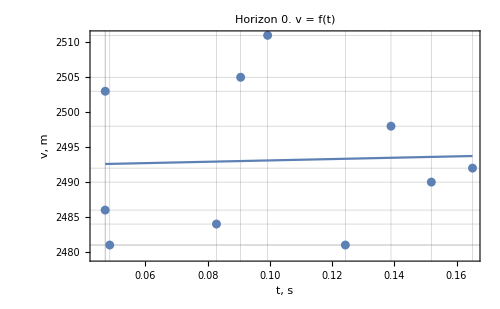
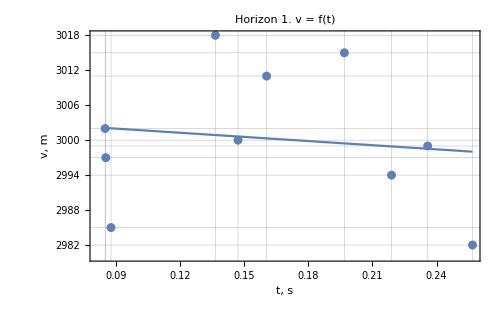
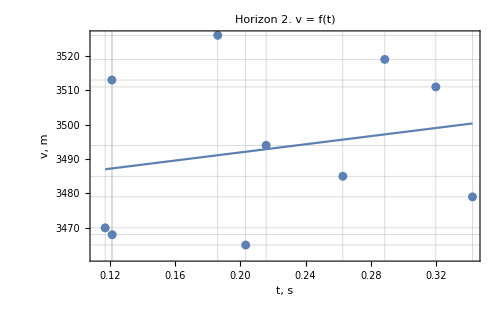

```mathematica
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

```mathematica
Clear[h]
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]]
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]]
resultTH=THMethod[wellDataset, time, h][["result"]]
```

{FittedModel[-0.0299747-0.000665276 h],FittedModel[-0.0370613-0.000962897 h],FittedModel[-0.0654548-0.00121482 h]}

{{-0.0299747,-0.000665276},{-0.0370613,-0.000962897},{-0.0654548,-0.00121482}}

{{{-232.,0.12426},{-274.,0.151898},{-293.,0.165131},{-253.,0.138935},{-194.,0.0992746},{-182.,0.090595},{-170.,0.0828291},{-118.,0.048511},{-115.,0.0470433},{-116.,0.0470672}},{{-243.,0.19691},{-286.,0.235872},{-304.,0.256832},{-263.,0.218954},{-205.,0.160545},{-194.,0.147174},{-181.,0.136603},{-129.,0.0877697},{-125.,0.0853343},{-128.,0.0850351}},{{-270.,0.262899},{-323.,0.32},{-327.,0.34251},{-282.,0.288636},{-233.,0.215785},{-236.,0.203258},{-212.,0.186075},{-148.,0.121055},{-141.,0.116941},{-160.,0.121252}}}

{{{40,-131.},{140,-173.},{240,-193.},{340,-152.},{440,-93.},{540,-80.},{640,-68.},{740,-17.},{840,-15.},{940,-15.}},{{0,-233.913},{10,-234.297},{20,-234.272},{30,-233.634},{40,-232.},{50,-229.852},{60,-230.852},{70,-228.776},{80,-232.401},{90,-233.038},{100,-237.528},{110,-244.353},{120,-254.63},{130,-263.202},{140,-274.},{150,-284.309},{160,-293.63},{170,-297.94},{180,-300.498},{190,-301.763},{200,-302.294},{210,-298.041},{220,-296.596},{230,-293.1},{240,-293.},{250,-295.173},{260,-295.223},{270,-294.265},{280,-293.644},{290,-290.749},{300,-286.566},{310,-277.573},{320,-269.095},{330,-260.498},{340,-253.},{350,-244.527},{360,-238.807},{370,-229.201},{380,-226.254},{390,-223.353},{400,-219.91},{410,-215.785},{420,-210.235},{430,-201.222},{440,-194.},{450,-183.698},{460,-175.438},{470,-169.173},{480,-165.101},{490,-160.048},{500,-157.78},{510,-162.957},{520,-173.971},{530,-176.342},{540,-182.},{550,-185.821},{560,-194.428},{570,-192.999},{580,-194.864},{590,-190.242},{600,-187.019},{610,-184.706},{620,-179.629},{630,-174.105},{640,-170.},{650,-165.083},{660,-153.448},{670,-147.08},{680,-138.094},{690,-128.165},{700,-121.767},{710,-117.015},{720,-115.708},{730,-116.801},{740,-118.},{750,-121.746},{760,-123.969},{770,-125.045},{780,-124.939},{790,-122.408},{800,-118.374},{810,-111.815},{820,-108.759},{830,-112.224},{840,-115.},{850,-119.459},{860,-128.527},{870,-141.05},{880,-148.569},{890,-155.583},{900,-158.484},{910,-155.678},{920,-146.651},{930,-133.192},{940,-116.},{950,-101.199},{960,-99.5597},{970,-97.8142},{980,-96.8914},{990,-96.8798},{1000,-96.8008}},{{0,-240.841},{10,-242.676},{20,-243.759},{30,-244.365},{40,-243.},{50,-240.881},{60,-242.343},{70,-241.207},{80,-245.439},{90,-247.291},{100,-252.507},{110,-260.812},{120,-269.613},{130,-276.873},{140,-286.},{150,-295.635},{160,-305.018},{170,-309.37},{180,-311.735},{190,-313.254},{200,-313.501},{210,-309.647},{220,-307.787},{230,-303.818},{240,-304.},{250,-306.497},{260,-305.551},{270,-302.665},{280,-302.195},{290,-298.482},{300,-294.346},{310,-285.559},{320,-277.467},{330,-269.689},{340,-263.},{350,-255.03},{360,-249.094},{370,-238.782},{380,-235.773},{390,-232.92},{400,-229.28},{410,-225.546},{420,-220.047},{430,-212.018},{440,-205.},{450,-194.634},{460,-186.806},{470,-181.002},{480,-177.917},{490,-174.2},{500,-171.211},{510,-177.338},{520,-187.717},{530,-189.406},{540,-194.},{550,-197.584},{560,-206.072},{570,-205.511},{580,-207.133},{590,-202.883},{600,-198.877},{610,-197.087},{620,-191.225},{630,-185.073},{640,-181.},{650,-175.929},{660,-164.26},{670,-157.265},{680,-148.52},{690,-138.761},{700,-132.662},{710,-128.43},{720,-127.348},{730,-127.839},{740,-129.},{750,-131.849},{760,-133.644},{770,-134.186},{780,-134.139},{790,-132.139},{800,-128.626},{810,-122.206},{820,-119.345},{830,-122.716},{840,-125.},{850,-129.084},{860,-138.577},{870,-151.175},{880,-158.227},{890,-165.014},{900,-167.56},{910,-165.374},{920,-157.01},{930,-144.183},{940,-128.},{950,-113.426},{960,-108.19},{970,-101.94},{980,-97.976},{990,-95.7984},{1000,-94.9087}},{{0,-255.163},{10,-260.002},{20,-263.928},{30,-267.653},{40,-270.},{50,-271.42},{60,-274.775},{70,-274.299},{80,-277.687},{90,-277.831},{100,-281.326},{110,-288.465},{120,-298.717},{130,-309.612},{140,-323.},{150,-335.021},{160,-345.237},{170,-350.123},{180,-349.792},{190,-346.035},{200,-344.059},{210,-336.981},{220,-334.244},{230,-328.689},{240,-327.},{250,-327.981},{260,-329.064},{270,-329.678},{280,-330.709},{290,-327.397},{300,-322.14},{310,-311.31},{320,-301.411},{330,-290.827},{340,-282.},{350,-273.693},{360,-268.634},{370,-261.187},{380,-258.999},{390,-257.359},{400,-255.603},{410,-252.406},{420,-247.633},{430,-239.129},{440,-233.},{450,-224.518},{460,-218.161},{470,-212.362},{480,-207.866},{490,-203.965},{500,-203.2},{510,-210.183},{520,-222.049},{530,-227.929},{540,-236.},{550,-240.51},{560,-247.167},{570,-244.807},{580,-244.451},{590,-238.572},{600,-233.218},{610,-229.796},{620,-223.911},{630,-217.812},{640,-212.},{650,-205.542},{660,-194.069},{670,-185.715},{680,-175.033},{690,-163.645},{700,-154.85},{710,-147.848},{720,-145.581},{730,-146.204},{740,-148.},{750,-153.443},{760,-156.729},{770,-158.142},{780,-157.015},{790,-152.238},{800,-145.556},{810,-138.337},{820,-135.107},{830,-137.323},{840,-141.},{850,-147.05},{860,-157.214},{870,-171.037},{880,-180.944},{890,-191.118},{900,-196.887},{910,-196.515},{920,-189.233},{930,-176.364},{940,-160.},{950,-144.602},{960,-138.781},{970,-133.645},{980,-131.778},{990,-132.178},{1000,-134.831}}}

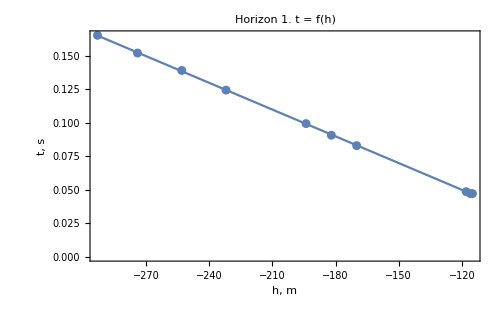
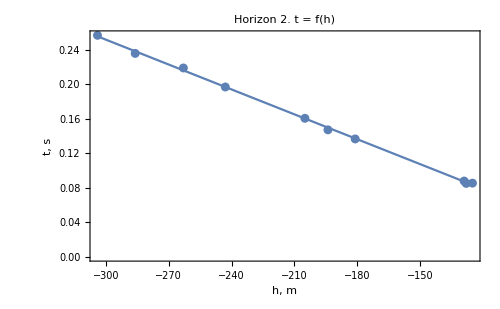
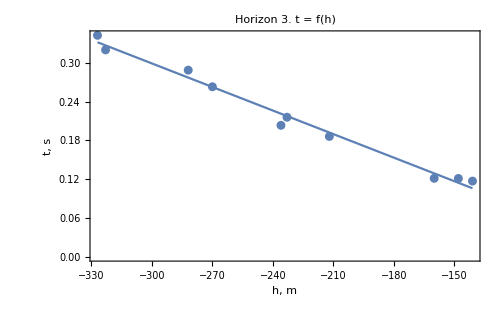

```mathematica
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]]
fitsVave = VaveMethod[wellDataset, time][["fits"]]
```

{2062.33,1319.13,1109.62}

{{{40,-131.},{140,-173.},{240,-193.},{340,-152.},{440,-93.},{540,-80.},{640,-68.},{740,-17.},{840,-15.},{940,-15.}},{{0,-238.894},{10,-238.586},{20,-237.55},{30,-235.523},{40,-232.},{50,-227.662},{60,-227.553},{70,-223.153},{80,-226.524},{90,-225.763},{100,-230.277},{110,-238.001},{120,-250.49},{130,-260.685},{140,-274.},{150,-286.73},{160,-298.209},{170,-302.939},{180,-305.407},{190,-306.266},{200,-306.302},{210,-299.976},{220,-297.726},{230,-292.902},{240,-293.},{250,-296.491},{260,-297.333},{270,-297.039},{280,-297.435},{290,-294.923},{300,-290.839},{310,-280.331},{320,-270.69},{330,-261.029},{340,-253.},{350,-243.737},{360,-238.32},{370,-227.6},{380,-226.005},{390,-224.424},{400,-222.007},{410,-218.527},{420,-212.921},{430,-202.356},{440,-194.},{450,-181.141},{460,-170.825},{470,-163.015},{480,-158.011},{490,-151.484},{500,-148.633},{510,-155.878},{520,-171.041},{530,-174.283},{540,-182.},{550,-187.192},{560,-198.976},{570,-197.048},{580,-199.729},{590,-193.63},{600,-189.604},{610,-187.011},{620,-180.842},{630,-174.307},{640,-170.},{650,-164.873},{660,-150.777},{670,-144.085},{680,-133.915},{690,-122.499},{700,-115.91},{710,-111.496},{720,-111.658},{730,-114.897},{740,-118.},{750,-124.266},{760,-128.128},{770,-130.137},{780,-130.275},{790,-126.872},{800,-121.224},{810,-111.966},{820,-107.398},{830,-111.695},{840,-115.},{850,-120.599},{860,-132.539},{870,-149.272},{880,-159.224},{890,-168.601},{900,-172.487},{910,-168.727},{920,-156.651},{930,-138.744},{940,-116.},{950,-96.8554},{960,-96.1187},{970,-95.6213},{980,-96.6704},{990,-99.4206},{1000,-102.563}},{{0,-243.724},{10,-245.34},{20,-245.891},{30,-245.739},{40,-243.},{50,-239.234},{60,-239.959},{70,-237.344},{80,-241.518},{90,-242.654},{100,-248.063},{110,-257.407},{120,-267.407},{130,-275.491},{140,-286.},{150,-297.222},{160,-308.205},{170,-312.892},{180,-315.164},{190,-316.484},{200,-316.325},{210,-311.107},{220,-308.584},{230,-303.561},{240,-304.},{250,-307.58},{260,-306.979},{270,-304.091},{280,-304.436},{290,-300.813},{300,-296.79},{310,-286.983},{320,-278.169},{330,-269.851},{340,-263.},{350,-254.589},{360,-248.804},{370,-237.476},{380,-235.409},{390,-233.5},{400,-230.52},{410,-227.323},{420,-221.76},{430,-212.828},{440,-205.},{450,-192.718},{460,-183.471},{470,-176.628},{480,-173.095},{490,-168.636},{500,-164.999},{510,-172.862},{520,-186.067},{530,-188.195},{540,-194.},{550,-198.528},{560,-209.31},{570,-208.648},{580,-210.829},{590,-205.641},{600,-200.876},{610,-199.058},{620,-192.221},{630,-185.192},{640,-181.},{650,-175.747},{660,-162.284},{670,-154.883},{680,-145.339},{690,-134.54},{700,-128.375},{710,-124.524},{720,-124.567},{730,-126.458},{740,-129.},{750,-133.454},{760,-136.348},{770,-137.45},{780,-137.628},{790,-135.172},{800,-130.661},{810,-122.351},{820,-118.473},{830,-122.448},{840,-125.},{850,-129.82},{860,-141.514},{870,-157.177},{880,-165.846},{890,-174.249},{900,-177.358},{910,-174.574},{920,-164.08},{930,-148.079},{940,-128.},{950,-110.17},{960,-104.431},{970,-97.6546},{980,-94.0566},{990,-93.0237},{1000,-93.9457}},{{0,-261.486},{10,-264.937},{20,-267.289},{30,-269.504},{40,-270.},{50,-269.387},{60,-271.527},{70,-268.648},{80,-271.128},{90,-269.389},{100,-272.321},{110,-280.324},{120,-292.686},{130,-306.079},{140,-323.},{150,-338.249},{160,-351.238},{170,-357.219},{180,-356.346},{190,-351.037},{200,-348.316},{210,-338.905},{220,-335.536},{230,-328.564},{240,-327.},{250,-329.232},{260,-331.788},{270,-333.881},{280,-336.693},{290,-333.79},{300,-328.391},{310,-315.592},{320,-304.145},{330,-291.855},{340,-282.},{350,-272.894},{360,-268.181},{370,-260.225},{380,-259.298},{390,-259.011},{400,-258.431},{410,-255.736},{420,-250.704},{430,-240.395},{440,-233.},{450,-222.124},{460,-213.836},{470,-206.074},{480,-199.888},{490,-194.374},{500,-193.003},{510,-202.044},{520,-217.679},{530,-225.308},{540,-236.},{550,-242.044},{560,-251.15},{570,-248.28},{580,-248.297},{590,-241.066},{600,-234.75},{610,-231.253},{620,-224.66},{630,-218.014},{640,-212.},{650,-205.357},{660,-192.148},{670,-183.279},{680,-171.349},{690,-158.482},{700,-149.07},{710,-141.972},{720,-141.097},{730,-143.897},{740,-148.},{750,-156.694},{760,-162.168},{770,-164.827},{780,-163.798},{790,-157.611},{800,-148.641},{810,-138.757},{820,-134.086},{830,-136.616},{840,-141.},{850,-148.493},{860,-161.464},{870,-179.328},{880,-191.896},{890,-204.835},{900,-211.867},{910,-210.681},{920,-200.263},{930,-182.42},{940,-160.},{950,-139.039},{960,-131.17},{970,-124.432},{980,-122.332},{990,-123.543},{1000,-128.074}}}

{{{0,-260.178},{10,-260.312},{20,-259.933},{30,-258.761},{40,-256.265},{50,-253.105},{60,-254.305},{70,-251.321},{80,-256.195},{90,-257.},{100,-263.122},{110,-272.475},{120,-286.592},{130,-298.391},{140,-313.265},{150,-327.487},{160,-340.368},{170,-346.39},{180,-350.018},{190,-351.882},{200,-352.746},{210,-347.05},{220,-345.21},{230,-340.554},{240,-340.556},{250,-343.671},{260,-343.868},{270,-342.674},{280,-341.932},{290,-338.059},{300,-332.406},{310,-320.137},{320,-308.56},{330,-296.801},{340,-286.531},{350,-274.902},{360,-267.029},{370,-253.806},{380,-249.7},{390,-245.641},{400,-240.82},{410,-235.049},{420,-227.307},{430,-214.8},{440,-204.737},{450,-190.437},{460,-178.931},{470,-170.16},{480,-164.4},{490,-157.299},{500,-154.031},{510,-160.993},{520,-175.984},{530,-179.141},{540,-186.837},{550,-192.045},{560,-203.85},{570,-201.91},{580,-204.51},{590,-198.225},{600,-193.871},{610,-190.773},{620,-183.886},{630,-176.383},{640,-170.821},{650,-164.135},{660,-148.225},{670,-139.535},{680,-127.25},{690,-113.671},{700,-104.941},{710,-98.4748},{720,-96.7428},{730,-98.3146},{740,-100.046},{750,-105.286},{760,-108.451},{770,-110.05},{780,-110.031},{790,-106.686},{800,-101.274},{810,-92.3911},{820,-88.3011},{830,-93.1425},{840,-97.0188},{850,-103.18},{860,-115.636},{870,-132.801},{880,-143.064},{890,-152.594},{900,-156.436},{910,-152.399},{920,-139.775},{930,-121.013},{940,-97.0682},{950,-76.3402},{960,-73.6003},{970,-70.6423},{980,-68.7362},{990,-67.9992},{1000,-67.0847}},{{0,-263.302},{10,-263.711},{20,-263.405},{30,-262.722},{40,-259.751},{50,-256.025},{60,-257.039},{70,-254.932},{80,-259.809},{90,-261.818},{100,-268.242},{110,-278.717},{120,-289.941},{130,-299.311},{140,-311.146},{150,-323.706},{160,-336.014},{170,-341.987},{180,-345.478},{190,-347.926},{200,-348.778},{210,-344.425},{220,-342.6},{230,-338.078},{240,-338.796},{250,-342.413},{260,-341.613},{270,-338.3},{280,-338.004},{290,-333.537},{300,-328.476},{310,-317.451},{320,-307.247},{330,-297.379},{340,-288.829},{350,-278.585},{360,-270.863},{370,-257.525},{380,-253.411},{390,-249.449},{400,-244.446},{410,-239.287},{420,-231.856},{430,-221.186},{440,-211.78},{450,-198.108},{460,-187.657},{470,-179.787},{480,-175.394},{490,-170.233},{500,-166.044},{510,-173.494},{520,-186.417},{530,-188.385},{540,-194.142},{550,-198.721},{560,-209.621},{570,-209.106},{580,-211.426},{590,-206.332},{600,-201.58},{610,-199.656},{620,-192.558},{630,-185.074},{640,-180.198},{650,-174.009},{660,-159.398},{670,-150.691},{680,-139.736},{690,-127.476},{700,-119.855},{710,-114.606},{720,-113.363},{730,-114.135},{740,-115.78},{750,-119.597},{760,-122.098},{770,-123.019},{780,-123.196},{790,-120.887},{800,-116.64},{810,-108.678},{820,-105.202},{830,-109.602},{840,-112.567},{850,-117.759},{860,-129.751},{870,-145.608},{880,-154.332},{890,-162.623},{900,-165.419},{910,-162.09},{920,-150.788},{930,-133.683},{940,-112.173},{950,-92.5527},{960,-84.6324},{970,-75.2534},{980,-68.5983},{990,-64.0228},{1000,-60.8848}},{{0,-296.074},{10,-294.988},{20,-293.725},{30,-293.183},{40,-291.718},{50,-289.876},{60,-291.458},{70,-288.629},{80,-291.704},{90,-291.042},{100,-295.471},{110,-305.328},{120,-319.837},{130,-335.61},{140,-355.078},{150,-372.982},{160,-388.668},{170,-397.328},{180,-399.051},{190,-396.195},{200,-395.719},{210,-388.282},{220,-386.556},{230,-380.83},{240,-380.056},{250,-382.573},{260,-384.927},{270,-386.368},{280,-388.114},{290,-383.765},{300,-376.575},{310,-361.676},{320,-347.853},{330,-332.949},{340,-320.276},{350,-308.182},{360,-300.348},{370,-289.169},{380,-284.953},{390,-281.346},{400,-277.446},{410,-271.468},{420,-263.223},{430,-249.805},{440,-239.439},{450,-225.763},{460,-214.867},{470,-204.711},{480,-196.363},{490,-188.941},{500,-185.936},{510,-193.636},{520,-208.246},{530,-215.183},{540,-225.539},{550,-231.606},{560,-241.036},{570,-238.718},{580,-239.441},{590,-232.995},{600,-227.47},{610,-224.697},{620,-218.686},{630,-212.408},{640,-206.472},{650,-199.568},{660,-185.8},{670,-176.141},{680,-163.254},{690,-149.329},{700,-138.822},{710,-130.659},{720,-128.815},{730,-130.806},{740,-134.325},{750,-142.707},{760,-148.115},{770,-150.908},{780,-150.166},{790,-144.374},{800,-135.862},{810,-126.453},{820,-122.226},{830,-125.126},{840,-129.76},{850,-137.335},{860,-150.177},{870,-167.653},{880,-179.53},{890,-191.428},{900,-197.024},{910,-193.96},{920,-181.178},{930,-160.439},{940,-134.544},{950,-109.484},{960,-96.8456},{970,-84.6231},{980,-76.2768},{990,-70.435},{1000,-67.0599}}}

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

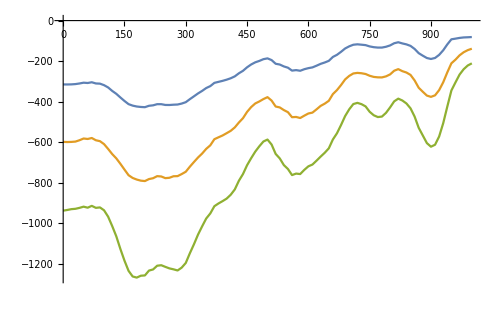

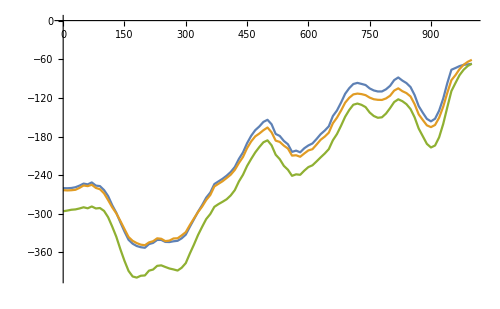

```mathematica
ListLinePlot[fitsVT]
ListLinePlot[fitsVave]
```

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-